```mathematica
sampling = 524288;
amplitude = Floor[(Power[2,16]-1)/4];
amplitude2={amplitude/2,amplitude,amplitude/2,amplitude}//N;
comSampling = sampling/2;
c=34000;
M=6;
SymNum=10;
Subscript[f, 0]=12000;
Subscript[f, 1]=18000;
k=(Subscript[f, 1]-Subscript[f, 0])/10/1000//N;
radian  = {0};
radius = 50;(*cm*)
Tx = {{-20,0},{20,0},{20,0}};
```

```mathematica
amplitude
```

16383

```mathematica
Clear[freq] ;
freq = {};
For[i=1,i≤6,i++,
AppendTo[freq,{14000 + i*1000-250, 14000+i*1000+250}];
]
```

```mathematica
SyncPattern[t_,freq1_,freq2_,ψ_,θ_]:=Sin[freq1 2Pi t + ψ] + Sin[freq2 2Pi t + ψ + θ];
```

```mathematica
g[n_]:=
If[n==0,0,
If[Mod[n,2]==1,Ceiling[SymNum/2],-(Ceiling[SymNum/2]-1)]
];
```

```mathematica
Clear[ψ];
ψ={};
Clear[tmp];
tmp={};
sum=0;
For[i=1,i≤SymNum,i++,
sum+=g[i-1];
AppendTo[tmp,2Pi sum/SymNum];
];
AppendTo[ψ,tmp];
Clear[tmp];
tmp = {};
For[i = 1, i≤SymNum, i++,
AppendTo[tmp,0];
];
AppendTo[ψ,tmp];
AppendTo[ψ,tmp];
```

```mathematica
Clear[θ];
θ={};
For[i=1,i≤SymNum,i++,
AppendTo[θ,Mod[(i-1)Pi/3,2Pi]];
]
```

```mathematica
ChirpSignal[t_]:=Sin[2Pi(Subscript[f, 0] + t k/2 )t]//N;
```

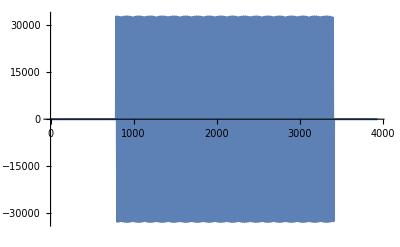

```mathematica
ListLinePlot[Table[If[t≥3/1000&&t≤13/1000,2amplitude ChirpSignal[t-3/1000]//N,0],{t,0,150/1000-1/comSampling,1/comSampling}][[;;Round[15 comSampling/1000]]],PlotRange->All]
```

```mathematica
Clear[pilot];
pilot={};
For[i=1,i≤3,i++,
If[i == 1||i == 3,
AppendTo[pilot,Table[If[t≥3/1000&&t≤13/1000,2amplitude ChirpSignal[t-3/1000]//N,0],{t,0,150/1000-1/comSampling,1/comSampling}]];Print[i],
AppendTo[pilot,Table[0.,{t,comSampling*150/1000 - 1/comSampling}]];Print[i];
];
Print[Length[pilot[[i]]]]
]
```

1

39321

2

39321

3

39321

```mathematica
comSampling(150/1000-1/comSampling)//N
```

39320.6

```mathematica
Length[pilot]
```

3

```mathematica
For[i = 1, i≤Length[radian],i++,
Clear[target];
target = {-radius Sin[radian[[i]]],radius Cos[radian[[i]]]};
Clear[ts];
ts={};
AppendTo[ts,0];
For[j=2,j≤Length[Tx],j++,
AppendTo[ts,(Norm[target-Tx[[j]]]-Norm[target-Tx[[1]]])/c//N];
];
Clear[SpotWave];
SpotWave={};
For[j=1,j≤Length[Tx],j++,
Clear[tmp];
tmp=pilot[[j]];
For[k=1,k≤SymNum,k++,
tmp2 =Table[
If[Mod[1000t,150]>3 -θ[[k]]/Pi-1000ts[[j]](*+50(j+Mod[j,2]-2)/2*)&&Mod[1000t,150]<7-θ[[k]]/Pi-1000ts[[j]](*+50(j+Mod[j,2]-2)/2*),
amplitude2[[j]] SyncPattern[t+ts[[j]],freq[[(j+Mod[j,2])/2+4,1]],freq[[(j+Mod[j,2])/2+4,2]],ψ[[j,k]],θ[[k]]],0]//N,
{t,(i-1)*150/1000,i*150/1000-1/comSampling,1/comSampling}
];
tmp=Join[tmp,tmp2];
];
AppendTo[SpotWave,tmp];
];
For[j=1,j≤Length[SpotWave],j++,
SpotWave[[j]]=Join[SpotWave[[j]],Table[0.,{t,2 comSampling-Length[SpotWave[[j]]]}]]//N;
];
SetDirectory["/home/yshoma/develop/workspace/octave/20190710/src/wave"];
For[j = 1, j ≤Length[Tx],j++,
If[radian[[i]]≠0,
Export["spotWave"<>ToString[j]<>"_"<>ToString[Pi/radian[[i]]]<>".txt",SpotWave[[j]]];
,
Export["spotWave"<>ToString[j]<>"_"<>ToString[radian[[i]]]<>".txt",SpotWave[[j]]];
];
];
]
```

```mathematica
Tx
```

{{-20,0},{20,0},{20,0}}

```mathematica
ListLinePlot[SpotWave[[1]]]
ListLinePlot[SpotWave[[2]]]
ListLinePlot[SpotWave[[3]]]
```

-Graphics-

-Graphics-

-Graphics-